```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_angular.dat","List"];
ww01 = Import["ww01_angular.dat","List"];
ww10 = Import["ww10_angular.dat","List"];
wwm10 = Import["wwm10_angular.dat","List"];
ww00 = Import["ww00_angular.dat","List"];
ww11 = Import["ww11_angular.dat","List"];
wwm1m1 = Import["wwm1m1_angular.dat","List"];
ww1m1 = Import["ww1m1_angular.dat","List"];
wwm11 = Import["wwm11_angular.dat","List"];
(*dyt import*)
dytww00 = Import["wwm00_angular_VLQ_01.dat","List"];
dytww11 = Import["ww11_angular_VLQ_01.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_VLQ_01.dat","List"];
dytww01 = Import["ww01_angular_VLQ_01.dat","List"];
dytww0m1 = Import["ww0m1_angular_VLQ_01.dat","List"];
dytww10 = Import["ww10_angular_VLQ_01.dat","List"];
dytwwm10 = Import["wwm10_angular_VLQ_01.dat","List"];
dytww1m1 = Import["ww1m1_angular_VLQ_01.dat","List"];
dytwwm11= Import["wwm11_angular_VLQ_01.dat","List"];
```

```mathematica
(*dyt import*)
(*dytww11 = Import["ww111_angular.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_dyt0.1_1000.dat","List"];
dytww1m1 = Import["ww1m1_angular_dyt0.1_1000.dat","List"];
dytwwm11 = Import["wwm11_angular_dyt0.1_1000.dat","List"];*)
sqrtsList=Table[350+25*i,{i,0,400}];
thetaList=Table[0+(Pi/180)*i,{i,0,181}];
```

```mathematica
ww00 [[181]]
```

9.97724×10^-7

```mathematica
<<CustomTicks.m
ticks0=LogTicks[10,-3,6,TickLabelStep->1];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

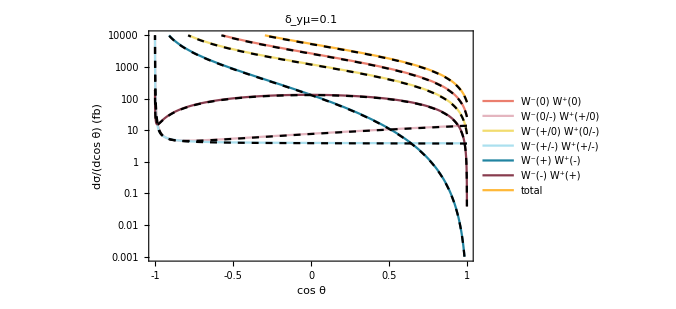

```mathematica
factor=0.3894*10^12;
lineplot=ListLogPlot[{Transpose[{Cos[thetaList],factor*ww00}],Transpose[{Cos[thetaList],factor*ww01}],Transpose[{Cos[thetaList],factor*ww10}],Transpose[{Cos[thetaList],factor*ww11}],Transpose[{Cos[thetaList],factor*ww1m1}],Transpose[{Cos[thetaList],factor*wwm11}],Transpose[{Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}], Transpose[{Cos[thetaList],factor*dytww00}],Transpose[{Cos[thetaList],factor*dytww01}],Transpose[{Cos[thetaList],factor*dytww10}],Transpose[{Cos[thetaList],factor*dytww11}],Transpose[{Cos[thetaList],factor*dytww1m1}],Transpose[{Cos[thetaList],factor*dytwwm11}],Transpose[{Cos[thetaList],factor*(2 dytww11 + dytwwm11 +  dytww1m1 + 2 dytww10  + 2 dytww01 + dytww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/(dcos θ) (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["δ_yμ=0.1",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.001,10000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
(*customticks package*)
```

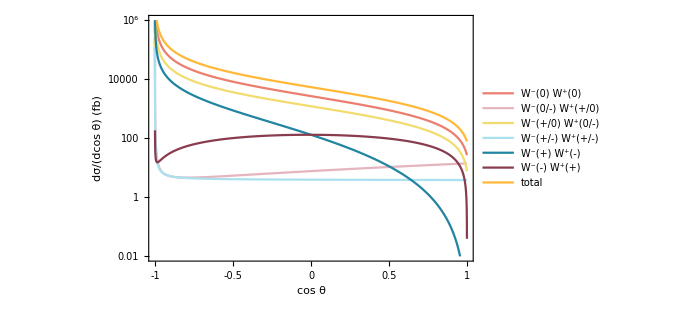

```mathematica
lineplot1=ListLogPlot[{Transpose[{Cos[thetaList],factor*ww00}],Transpose[{Cos[thetaList],factor*ww01}],Transpose[{Cos[thetaList],factor*ww10}],Transpose[{Cos[thetaList],factor*ww11}],Transpose[{Cos[thetaList],factor*ww1m1}],Transpose[{Cos[thetaList],factor*wwm11}],Transpose[{Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/(dcos θ) (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
(*Export["WWtt_angular_partonic.pdf",lineplot1]
```

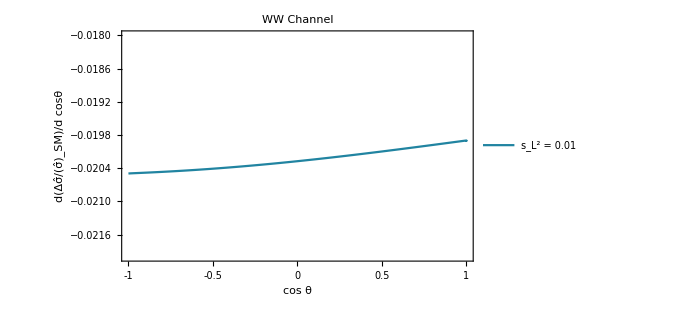

```mathematica
nonlinearlineplot3=ListPlot[{Transpose[{-Cos[thetaList],( dytww11 + dytww00+dytwwm1m1+dytww01+dytww0m1+dytww10+dytwwm10+dytww1m1+dytwwm11-ww11  - ww00 - wwm1m1 - ww10 - wwm10 - ww01 - ww0m1 - ww1m1 - wwm11)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][6],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,20,FontFamily->"Times"],Style["d(Δσ̂/(σ̂)_SM)/d cosθ",Black,18,FontFamily->"Times"]},
PlotLabel->Style["WW Channel",Black,18],
PlotLegends->Placed[{Style[" s_L^2 =    0.01 ",Black,18,FontFamily->"Times"],Style[" δ_yt = - 0.015",Black,18,FontFamily->"Times"]},{0.76,0.8}],
PlotRange->{{-1,1},{-0.018,-0.022}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
Export["angular_sb_VLQ.pdf",nonlinearlineplot3]
```

angular_sb_VLQ.pdf

Show::gcomb: Could not combine the graphics objects in Show[,linearlineplot3].

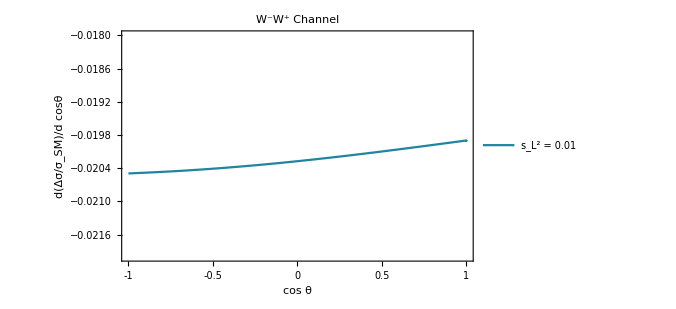
Show[-Graphics-,linearlineplot3]

```mathematica
combinedcos = Show[nonlinearlineplot3, linearlineplot3]
```

```mathematica
Export["WWcombined_angular.pdf",combinedcos]
```

WWcombined_angular.pdf

```mathematica
(*Export["WWtt_angular_partonic_dyt2.pdf",lineplot3]
```

```mathematica
(*Export["WW_angular_1000_total.pdf",lineplot3]
```

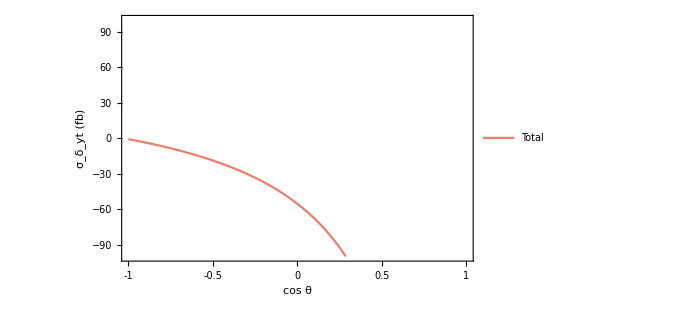

```mathematica
lineplot4=ListPlot[{Transpose[{-Cos[thetaList],factor*(2 dytww11 + dytww00-2 ww11  - ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["σ_δ_yt (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" Total",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{-100,100}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
factor*(2 dytww11 + dytww00-2 ww11  - ww00)
```

{-0.741014,-0.74513,-0.757481,-0.778073,-0.806921,-0.844042,-0.889458,-0.943197,-1.00529,-1.07579,-1.15472,-1.24214,-1.33811,-1.44268,-1.55592,-1.6779,-1.8087,-1.9484,-2.09709,-2.25487,-2.42184,-2.5981,-2.78378,-2.97899,-3.18387,-3.39854,-3.62316,-3.85786,-4.10282,-4.35819,-4.62416,-4.9009,-5.18862,-5.4875,-5.79776,-6.11963,-6.45333,-6.7991,-7.1572,-7.5279,-7.91146,-8.30817,-8.71834,-9.14228,-9.58032,-10.0328,-10.5001,-10.9825,-11.4805,-11.9945,-12.5248,-13.072,-13.6365,-14.2187,-14.8193,-15.4386,-16.0772,-16.7358,-17.4149,-18.1151,-18.8372,-19.5817,-20.3493,-21.1409,-21.9572,-22.7991,-23.6672,-24.5627,-25.4863,-26.4391,-27.4221,-28.4363,-29.4828,-30.563,-31.6779,-32.8288,-34.0172,-35.2444,-36.512,-37.8214,-39.1744,-40.5727,-42.0181,-43.5125,-45.0579,-46.6565,-48.3105,-50.0223,-51.7944,-53.6293,-55.53,-57.4992,-59.5402,-61.6562,-63.8506,-66.1273,-68.49,-70.9429,-73.4904,-76.1373,-78.8883,-81.7489,-84.7247,-87.8216,-91.046,-94.4047,-97.9051,-101.555,-105.362,-109.336,-113.487,-117.823,-122.357,-127.101,-132.066,-137.267,-142.719,-148.437,-154.439,-160.743,-167.37,-174.342,-181.682,-189.418,-197.576,-206.189,-215.289,-224.914,-235.105,-245.907,-257.368,-269.543,-282.492,-296.282,-310.985,-326.685,-343.472,-361.449,-380.73,-401.443,-423.734,-447.766,-473.725,-501.82,-532.293,-565.418,-601.512,-640.939,-684.121,-731.55,-783.8,-841.546,-905.586,-976.866,-1056.52,-1145.91,-1246.68,-1360.86,-1490.93,-1639.97,-1811.86,-2011.52,-2245.24,-2521.24,-2850.34,-3247.08,-3731.3,-4330.7,-5084.83,-6051.74,-7319.41,-9026.23,-11400.,-14836.4,-20071.5,-28597.6,-43797.9,-74567.5,-148901.,-345521.,-12171.8,-345521.}